# diffusion constant via GK

```mathematica
p0s={3.85,3.825,3.80,3.75};
```

```mathematica
temperatures={{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022},{0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};(*id for configurations*)
```

```mathematica
(*The dimentionas are {p0,T,id}*)
finalD={{0.0440.004,0.01440.0013,0.00830.0005,0.003770.00034,0.00290.0005,0.001680.00024,0.001130.00014,0.000480.00008,0.0001690.000026,0.0000880.000011,0.0000539,0.000020915,9.11.510^-6,6.80.810^-6,4.11.010^-6,2.70.510^-6,1.880.1710^-6},{0.06690.0023,0.03680.0019,0.02540.0016,0.01040.0007,0.00530.0006,0.00380.0005,0.002580.00015,0.001910.00024,0.001290.00012,0.000990.00015,0.000630.00009,0.000460.00005,0.0002620.000032,0.0001020.000014,0.0000324,0.000013013},{0.05870.0028,0.02990.0024,0.02010.0015,0.01400.0007,0.006540.00030,0.002900.00034,0.001810.00019,0.001080.00011,0.000690.00009,0.000330.00006,0.0001340.000015,0.0000890.000010,0.0000526,0.000028827},{0.04160.0013,0.01750.0012,0.01150.0010,0.00690.0005,0.00400.0004,0.001860.00020,0.001070.00007,0.000390.00004,0.0001740.000027,0.0000599,0.000023832}};
```

```mathematica
p0s[[2]]
temperatures[[2,11]]
finalD[[2,11]]
```

3.825

0.0025

0.000630.00009

```mathematica
data=Table[test=Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/velocityCorrelation/velocityCorrelation_N4096_p3.8250_T0.00250000_dt0.01_idx"<>ToString[i]<>".nc","CSV"];0.01/2*Total[Most[Flatten[Normal[test]]]+Rest[Flatten[Normal[test]]]],{i,10,19}]
```

{-0.000137048,0.00091795,-0.000766272,0.00493501,0.00176846,0.00324748,-0.0000987428,0.00836327,0.00106498,-0.000480399}

```mathematica
Mean[data]/2
```

0.000940734

```mathematica
test=Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/velocityCorrelation/velocityCorrelation_N4096_p3.8250_T0.00250000_dt0.01_idx11.nc","CSV"];
```

```mathematica
0.01/2*Total[Most[Flatten[Normal[test]]]+Rest[Flatten[Normal[test]]]]
```

0.00091795

```mathematica
Table[0.01/2*Total[Most[Flatten[Normal[test]][[;;-Ceiling[i*Length[test]]]]]+Rest[Flatten[Normal[test]][[;;-Ceiling[i*Length[test]]]]]],{i,0.1,0.5,0.1}]
```

{0.00248516,0.00372128,0.00305523,0.00104133,-0.0000313171}

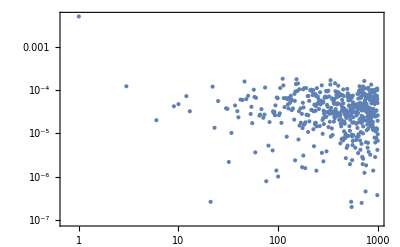

```mathematica
ListLogLogPlot[Flatten[Normal[data]][[;;;;1000]]]
```

```mathematica
diffusion=0.01/2*Total[Most[Flatten[Normal[data]]]+Rest[Flatten[Normal[data]]]]
```

0.00091795